Exercises for Section 33 | Expressions and Their Structure

Find the head of the output from ListPlot. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Head@ListPlot[{1,2}]
```

Graphics

Use @@ to compute the result of multiplying together integers up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Times@@Table[n,{n,100}]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

Use @@@ and Tuples to generate {f[a,a],f[a,b],f[b,a],f[b,b]}. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

Make a list of tree forms for the results of 4 successive applications of #^#& starting from x. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FoldList[#^#&,4][x]
```

FoldList::normal: Nonatomic expression expected at position 2 in FoldList[#1^#1&,4].

FoldList[#1^#1&,4][x]

```mathematica
Function[Slot[1]^Slot[1]][x]
```

x^x

```mathematica
TreeForm/@NestList[#^#&,x,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Find the unique cases where i^2/(j^2+1) is an integer, with i and j going up to 20. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Cases[Table[i^2/(j^2+1),{i,20},{j,20}],Real]
```

{}

```mathematica
DeleteDuplicates[Sort@Cases[Flatten@Table[i^2/(j^2+1),{i,20},{j,20}],_Integer]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

Create a graph that connects successive pairs of numbers in Table[Mod[n^2+n,100],{n,100}]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Mod[n^2+n,100],{n,100}]
```

{2,6,12,20,30,42,56,72,90,10,32,56,82,10,40,72,6,42,80,20,62,6,52,0,50,2,56,12,70,30,92,56,22,90,60,32,6,82,60,40,22,6,92,80,70,62,56,52,50,50,52,56,62,70,80,92,6,22,40,60,82,6,32,60,90,22,56,92,30,70,12,56,2,50,0,52,6,62,20,80,42,6,72,40,10,82,56,32,10,90,72,56,42,30,20,12,6,2,0,0}

```mathematica
Partition[Table[Mod[n^2+n,100],{n,100}],2,1]
```

{{2,6},{6,12},{12,20},{20,30},{30,42},{42,56},{56,72},{72,90},{90,10},{10,32},{32,56},{56,82},{82,10},{10,40},{40,72},{72,6},{6,42},{42,80},{80,20},{20,62},{62,6},{6,52},{52,0},{0,50},{50,2},{2,56},{56,12},{12,70},{70,30},{30,92},{92,56},{56,22},{22,90},{90,60},{60,32},{32,6},{6,82},{82,60},{60,40},{40,22},{22,6},{6,92},{92,80},{80,70},{70,62},{62,56},{56,52},{52,50},{50,50},{50,52},{52,56},{56,62},{62,70},{70,80},{80,92},{92,6},{6,22},{22,40},{40,60},{60,82},{82,6},{6,32},{32,60},{60,90},{90,22},{22,56},{56,92},{92,30},{30,70},{70,12},{12,56},{56,2},{2,50},{50,0},{0,52},{52,6},{6,62},{62,20},{20,80},{80,42},{42,6},{6,72},{72,40},{40,10},{10,82},{82,56},{56,32},{32,10},{10,90},{90,72},{72,56},{56,42},{42,30},{30,20},{20,12},{12,6},{6,2},{2,0},{0,0}}

```mathematica
Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]
```

{2→6,6→12,12→20,20→30,30→42,42→56,56→72,72→90,90→10,10→32,32→56,56→82,82→10,10→40,40→72,72→6,6→42,42→80,80→20,20→62,62→6,6→52,52→0,0→50,50→2,2→56,56→12,12→70,70→30,30→92,92→56,56→22,22→90,90→60,60→32,32→6,6→82,82→60,60→40,40→22,22→6,6→92,92→80,80→70,70→62,62→56,56→52,52→50,50→50,50→52,52→56,56→62,62→70,70→80,80→92,92→6,6→22,22→40,40→60,60→82,82→6,6→32,32→60,60→90,90→22,22→56,56→92,92→30,30→70,70→12,12→56,56→2,2→50,50→0,0→52,52→6,6→62,62→20,20→80,80→42,42→6,6→72,72→40,40→10,10→82,82→56,56→32,32→10,10→90,90→72,72→56,56→42,42→30,30→20,20→12,12→6,6→2,2→0,0→0}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

Generate a graph showing which word can follow which in the first 200 words of the Wikipedia article on computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Rule@@@Partition[Take[TextWords[WikipediaData["computers"]],200],2,1]
```

{A→computer,computer→is,is→a,a→digital,digital→electronic,electronic→machine,machine→that,that→can,can→be,be→programmed,programmed→to,to→carry,carry→out,out→sequences,sequences→of,of→arithmetic,arithmetic→or,or→logical,logical→operations,operations→computation,computation→automatically,automatically→Modern,Modern→computers,computers→can,can→perform,perform→generic,generic→sets,sets→of,of→operations,operations→known,known→as,as→programs,programs→These,These→programs,programs→enable,enable→computers,computers→to,to→perform,perform→a,a→wide,wide→range,range→of,of→tasks,tasks→A,A→computer,computer→system,system→is,is→a,a→complete,complete→computer,computer→that,that→includes,includes→the,the→hardware,hardware→operating,operating→system,system→main,main→software,software→and,and→peripheral,peripheral→equipment,equipment→needed,needed→and,and→used,used→for,for→full,full→operation,operation→This,This→term,term→may,may→also,also→refer,refer→to,to→a,a→group,group→of,of→computers,computers→that,that→are,are→linked,linked→and,and→function,function→together,together→such,such→as,as→a,a→computer,computer→network,network→or,or→computer,computer→cluster,cluster→A,A→broad,broad→range,range→of,of→industrial,industrial→and,and→consumer,consumer→products,products→use,use→computers,computers→as,as→control,control→systems,systems→Simple,Simple→special-purpose,special-purpose→devices,devices→like,like→microwave,microwave→ovens,ovens→and,and→remote,remote→controls,controls→are,are→included,included→as,as→are,are→factory,factory→devices,devices→like,like→industrial,industrial→robots,robots→and,and→computer-aided,computer-aided→design,design→as,as→well,well→as,as→general-purpose,general-purpose→devices,devices→like,like→personal,personal→computers,computers→and,and→mobile,mobile→devices,devices→like,like→smartphones,smartphones→Computers,Computers→power,power→the,the→Internet,Internet→which,which→links,links→billions,billions→of,of→other,other→computers,computers→and,and→users,users→Early,Early→computers,computers→were,were→meant,meant→to,to→be,be→used,used→only,only→for,for→calculations,calculations→Simple,Simple→manual,manual→instruments,instruments→like,like→the,the→abacus,abacus→have,have→aided,aided→people,people→in,in→doing,doing→calculations,calculations→since,since→ancient,ancient→times,times→Early,Early→in,in→the,the→Industrial,Industrial→Revolution,Revolution→some,some→mechanical,mechanical→devices,devices→were,were→built,built→to,to→automate,automate→long,long→tedious,tedious→tasks,tasks→such,such→as,as→guiding,guiding→patterns,patterns→for,for→looms,looms→More,More→sophisticated,sophisticated→electrical}

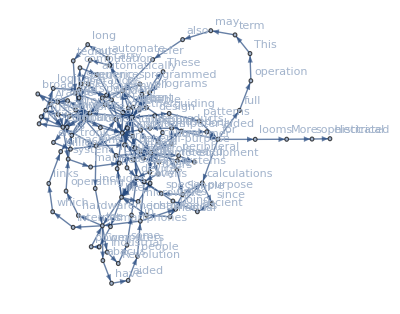

```mathematica
Graph[Rule @@@ 
  Partition[Take[TextWords[WikipediaData["computers"]], 200], 2, 1], 
 VertexLabels -> All]
```

```mathematica
Graph[Rule @@@ 
  Partition[TextWords[WikipediaData["computers"], 200], 2, 1], 
 VertexLabels -> All]
```

-Graphics-

Find a simpler form for f@@#&/@{{1,2},{7,2},{5,4}}. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
f@@#&/@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

```mathematica
f @@@ {{1, 2}, {7, 2}, {5, 4}}
```

{f[1,2],f[7,2],f[5,4]}